```mathematica
SetDirectory[NotebookDirectory[]];
(files=FileNames["data/*.ods"])//TableForm
Needs["ErrorBarPlots`"]
Needs["ErrorBarPlots`"]
yagvsdiode=First@Import[files[[1]]];
yagvsdiode=yagvsdiode[[1;;25]];
zweite=First@Import@files[[4]];
zweite=zweite[[1;;22]];
frequenz=First@Import@files[[2]];
frequenz=frequenz[[1;;24]];
pockels=First@Import@files[[3]];
pockels=pockels[[1;;21]];
PowerVsI={{200,41.9,0.1},{350,197,1},{500,359,2}};
```

data/erstemessung.ods
data/frequenzdoppel.ods
data/pockel.ods
data/zweitemesseung.ods

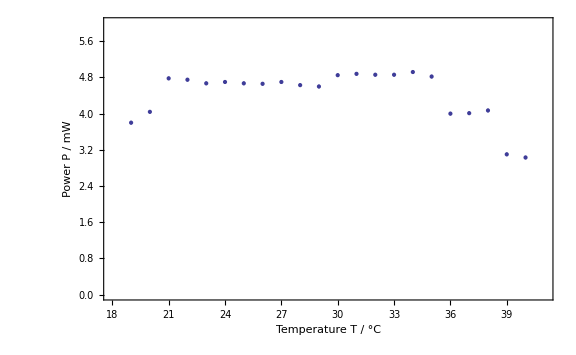

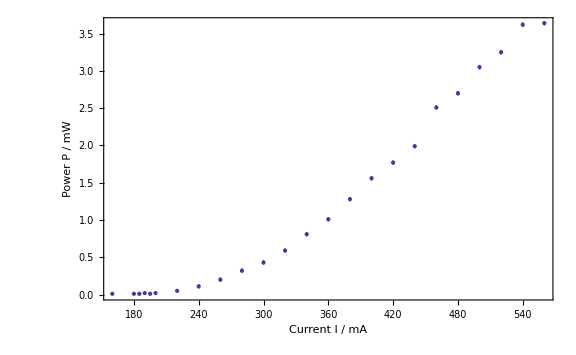

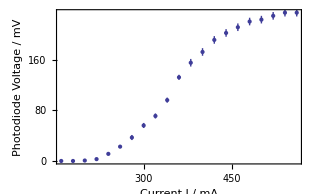

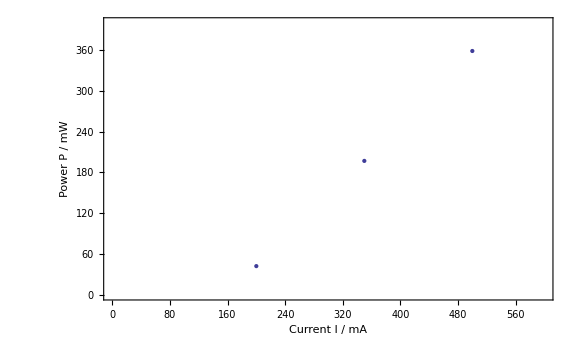

```mathematica
Show[ErrorListPlot[zweite,PlotRange->{{18,41},{0,6}}],ImageSize->Large,Frame->True,FrameLabel->{"Temperature T / °C","Power P / mW"},Axes->None]
Show[ErrorListPlot[frequenz],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
Show[ErrorListPlot[pockels],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Photodiode Voltage / mV"},Axes->None]
Show[ErrorListPlot[PowerVsI,PlotRange->{{0,600},{0,400}}],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

| Wert | Fehler
Steigung b | 1.04554 | 0.00474045
Achsenabschnitt a | -167.217 | 0.963763

Anzahl n: 3, R^2: 0.999878, χ^2/(n - 2): 5.94382

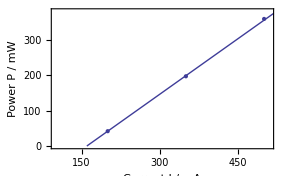

```mathematica
setz=LinReg[PowerVsI];
Show[Plot[(b*x+a/.setz),{x,0,520},PlotRange->{{100,510},{0,380}}],ErrorListPlot[PowerVsI],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

```mathematica
-167.21722846441946/1.0455430711610487
```

-159.933

```mathematica
b=1.045543071161048;
db=0.005;
da=0.96;
a=-159.933371543201;
```

```mathematica
YAG POWER VS DIODE POWER
```

```mathematica
Show[ErrorListPlot[yagvsdiode],ImageSize->Large,Frame->True,FrameLabel->{"Current I / mA","Power P / mW"},Axes->None]
```

```mathematica
yagvsdiode//TableForm
```

```mathematica
{{140, 0.07, 0.01}, {160, 0.07, 0.01}, {180, 0.07, 0.01}, {200, 0.23, 0.01}, {190, 0.14, 0.01}, {185, 0.09, 0.01}, {195, 0.18, 0.01}, {220, 0.45, 0.01}, {240, 0.7, 0.01}, {260, 0.96, 0.01}, {280, 1.21, 0.01}, {300, 1.56, 0.01}, {320, 1.85, 0.01}, {340, 2.2, 0.01}, {360, 2.6, 0.01}, {380, 2.89, 0.01}, {400, 3.28, 0.03}, {420, 3.56, 0.03}, {440, 4, 0.03}, {460, 4.3, 0.03}, {480, 4.6, 0.03}, {500, 4.89, 0.03}, {520, 5.08, 0.03}, {540, 5.27, 0.03}, {560, 5.6, 0.03}}
```

```mathematica
yagvsdiodcal=Table[{0,0,0,0},{i,Length[yagvsdiode]}];
```

```mathematica
For[i=1,i≤Length[yagvsdiodcal],i++,yagvsdiodcal[[i,1]]=((yagvsdiode[[i,1]]+a)*b);yagvsdiodcal[[i,2]]=-b*da+(yagvsdiode[[i,1]]-a)*db;yagvsdiodcal[[i,3]]=yagvsdiode[[i,2]];yagvsdiodcal[[i,4]]=yagvsdiode[[i,3]]]
Lins={#[[1]],#[[3]]}&/@yagvsdiodcal;
```

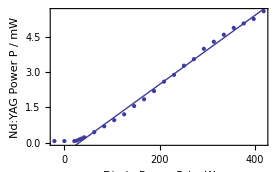

```mathematica
hund=Normal@LinearModelFit[Lins[[4;;25]],x,x];
katze=Normal@LinearModelFit[Lins[[4;;10]],x,x];
Show[ErrorListPlot[({{#[[1]],#[[3]]},ErrorBar[#[[2]],#[[4]]]}&/@yagvsdiodcal)],Plot[hund,{x,-100,500}],ImageSize->Large,Frame->True,FrameLabel->{"Diode Power P / mW","Nd:YAG Power P / mW"},Axes->None]
```

```mathematica
LinearModelFit[Lins[[4;;25]],x,x]["ParameterConfidenceIntervalTable"]//TableForm
```

| Estimate | Standard Error | Confidence Interval
1 | -0.454639 | 0.0467492 | {-0.552156,-0.357122}
x | 0.0146982 | 0.000195488 | {0.0142904,0.015106}

```mathematica
LinRegVar[Lins[[4;;25]]]
```

| Wert | Fehler
Steigung b | 0.0146982 | 0.000195488
Achsenabschnitt a | -0.454639 | 0.0467492

{1.04554→0.0146982,Δb→0.000195488,-159.933→-0.454639,Δa→0.0467492,n→22,R2→0.996475,NAME→,dataset→{{41.8914,0.23},{31.436,0.14},{26.2082,0.09},{36.6637,0.18},{62.8022,0.45},{83.7131,0.7},{104.624,0.96},{125.535,1.21},{146.446,1.56},{167.357,1.85},{188.267,2.2},{209.178,2.6},{230.089,2.89},{251.,3.28},{271.911,3.56},{292.822,4},{313.733,4.3},{334.643,4.6},{355.554,4.89},{376.465,5.08},{397.376,5.27},{418.287,5.6}}}

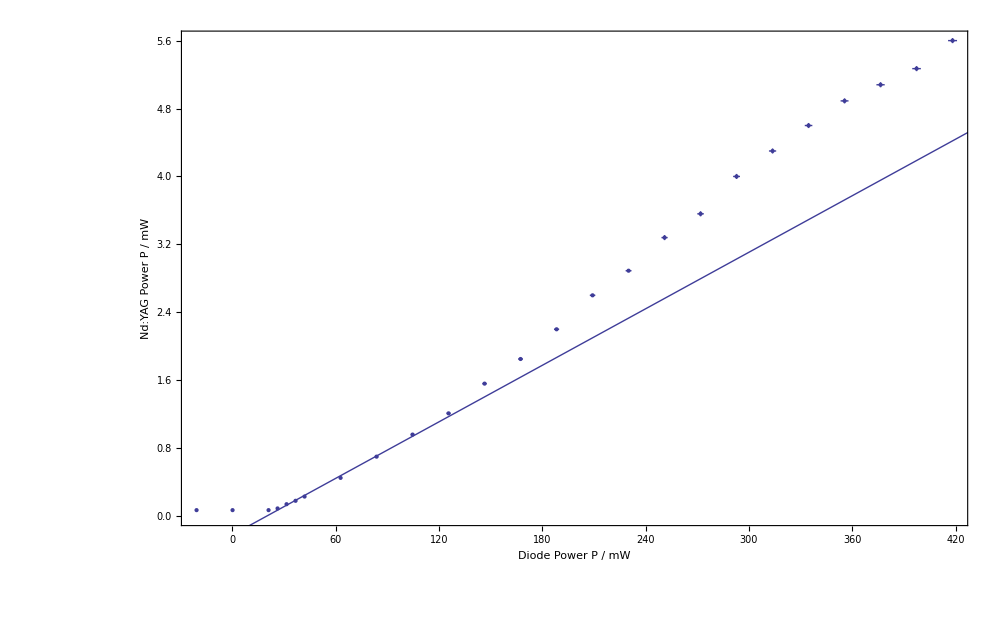

```mathematica
hund=Normal@LinearModelFit[Lins[[4;;10]],x,x];
katze=Normal@LinearModelFit[Lins[[4;;10]],x,x];
Show[ErrorListPlot[({{#[[1]],#[[3]]},ErrorBar[#[[2]],#[[4]]]}&/@yagvsdiodcal)],Plot[hund,{x,-100,500}],ImageSize->Large,Frame->True,FrameLabel->{"Diode Power P / mW","Nd:YAG Power P / mW"},Axes->None]
```

```mathematica
TEMPERATUR BLA
```

```mathematica
plateau temperatur 21 und 35 grad entsprechen bei 500mA
```

```mathematica
0.309*21+798.4
```

804.889

```mathematica
0.309*35+798.4
```

809.215

```mathematica
EICHUNG
```

```mathematica
yagvsdiodeeich={{160,0.07,0.01},{180,0.07,0.01},{200,0.23,0.01},{220,0.45,0.01},{240,0.7,0.01},{260,0.96,0.01},{280,1.21,0.01},{300,1.56,0.01},{320,1.85,0.01},{340,2.2,0.01},{360,2.6,0.01},{380,2.89,0.01},{400,3.28,0.03},{420,3.56,0.03},{440,4,0.03},{460,4.3,0.03},{480,4.6,0.03},{500,4.89,0.03},{520,5.08,0.03},{540,5.27,0.03},{560,5.6,0.03}};
```

```mathematica
photoeich=yagvsdiodeeich;
For[i=1,i≤Length[yagvsdiodeeich],i++,photoeich[[i,1]]=pockels[[i,2]];photoeich[[i,2]]=yagvsdiodeeich[[i,2]]]
```

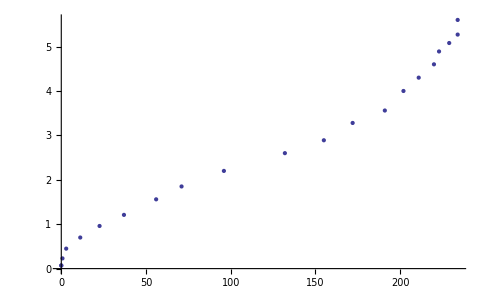

```mathematica
ErrorListPlot[{photoeich}]
```

```mathematica
eichforfit={{0,0.07},{0.7,0.23},{2.9,0.45},{11.2,0.7},{22.6,0.96},{37,1.21},{56,1.56},{71,1.85},{96,2.2},{132,2.6},{155,2.89},{172,3.28},{191,3.56},{202,4},{211,4.3},{220,4.6},{223,4.89},{229,5.08},{234,5.6}};
```

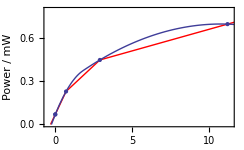

```mathematica
f=Interpolation[eichforfit[[1;;4]],InterpolationOrder->1,Method->"Spline"];
f2=Interpolation[eichforfit[[1;;4]],InterpolationOrder->2,Method->"Spline"];
Show[Plot[f[x],{x,-0.5,12.0},PlotRange->{{-0.5,11.4},{0,0.8}},PlotStyle->Red],Plot[f2[x],{x,-0.5,12.0},PlotRange->{{-0.5,11.4},{0,0.8}}],ErrorListPlot[photoeich],ImageSize->Large,Frame->True,FrameLabel->{"Photodiode Current / mV","Power / mW"},Axes->None]
```

```mathematica
Unset[error]
error[x_]:=((f2[x]-f[x])/f2[x]);
Plot[error[x],{x,0,4}]
```

```mathematica
f[0.05]
```

0.083167

```mathematica
FREQUENZDOPPLUNG
```

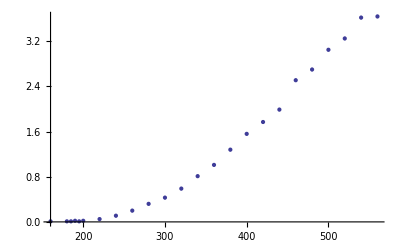

```mathematica
ErrorListPlot[frequenz]
```

160 | 0.0726567 | 0.00510573
180 | 0.0726567 | 0.00510573
185 | 0.0726567 | 0.00510573
190 | 0.0753026 | 0.00970986
195 | 0.0726567 | 0.00510573
200 | 0.0753026 | 0.00970986
220 | 0.0831759 | 0.0210073
240 | 0.0986321 | 0.0353762
260 | 0.121091 | 0.0443991
280 | 0.14968 | 0.043677
300 | 0.174528 | 0.0357645
320 | 0.208346 | 0.0167472
340 | 0.250353 | 0.0373576
360 | 0.284024 | 0.0810633
380 | 0.322658 | 0.107413
400 | 0.354443 | 0.10846
420 | 0.37275 | 0.0959076
440 | 0.388637 | 0.0762577
460 | 0.424523 | 0.0318545
480 | 0.437089 | 0.0162182
500 | 0.459471 | 0.010779
520 | 0.471815 | 0.0238919
540 | 0.493797 | 0.0447756
560 | 0.494953 | 0.0457907

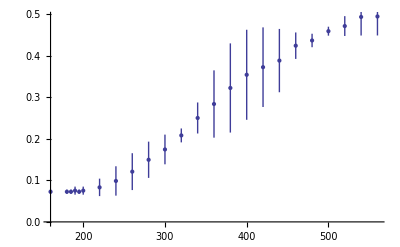

```mathematica
frequenzeich=frequenz;
For[i=1,i≤Length[frequenz],i++,frequenzeich[[i,2]]=f2[frequenz[[i,2]]]//N;frequenzeich[[i,3]]=error[frequenz[[i,2]]]//N];
frequenzeich//TableForm
ErrorListPlot[frequenzeich]
```

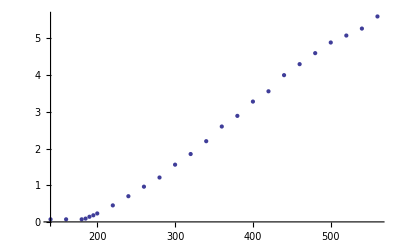

```mathematica
ErrorListPlot[yagvsdiode]
```

FittedModel[0.068482+4.97022×10^-6 x^2]

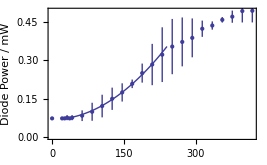

```mathematica
frequenzvsdiode=Table[{0,0,0,0},{i,Length[frequenzeich]}];
For[i=1,i≤Length[frequenzeich],i++,frequenzvsdiode[[i,1]]=((frequenzeich[[i,1]]+a)*b);frequenzvsdiode[[i,2]]=-b*da+(frequenzeich[[i,1]]-a)*db;frequenzvsdiode[[i,3]]=frequenzeich[[i,2]];frequenzvsdiode[[i,4]]=frequenzeich[[i,3]]];

frequenzvalues={#[[1]],#[[3]]}&/@frequenzvsdiode;
frequenzerrors=#[[4]]&/@frequenzvsdiode;
fit=NonlinearModelFit[frequenzvalues[[2;;15]],w*(x)^2+c,{w,q,c},x,Weights->1/frequenzerrors[[2;;15]]^2]
Show[ErrorListPlot[({{#[[1]],#[[3]]},ErrorBar[#[[2]],#[[4]]]}&/@frequenzvsdiode)],Plot[Normal@fit,{x,20,240}],ImageSize->Large,Frame->True,FrameLabel->{"Diode Power / mV","Laser Power / mW"},Axes->None]
```

FittedModel[0.0715835+5.91824×10^-6 (-15.6362+x)^2]

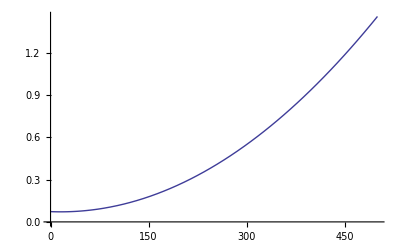

```mathematica
frequenzvalues={#[[1]],#[[3]]}&/@frequenzvsdiode;
frequenzerrors=#[[4]]&/@frequenzvsdiode;
fit=NonlinearModelFit[frequenzvalues[[1;;15]],w*(x-q)^2+c,{q,w,c},x,Weights->1/frequenzerrors[[1;;15]]^2]
Plot[Normal@fit,{x,0,500}]
```